# Figure 1

```mathematica
localdir="C:\\Users\\tramiada\\OneDrive\\Projects\\gen_spe\\Figure1\\" ;
```

## Figure 1 landscape

### Default

```mathematica
SeedRandom[4];

Lsize = 6;

λ = 0.2; γ = 1; τ = 100; 
totru = π  λ^2 γ τ Lsize^2;

patchxy =RandomReal[{0,Lsize},{γ Lsize^2,2}] ;
patchq =RandomReal[{0,1},γ Lsize^2] ;
patchxyq= Partition[Flatten[Riffle[patchxy,patchq]],3];

resunit ={};
Do[
xy =RandomChoice[patchxyq,1][[1]];
x = xy[[1]];
y = xy[[2]];
q = xy[[3]];

r = λ* Sqrt@RandomReal[];
theta = RandomReal[{0,2π},1];

newx = x + r Cos[theta];
newy = y + r Sin[theta];
newq= RandomReal[];

ru  =Flatten@{x,y,q, newx, newy,newq};
AppendTo[resunit,ru];
,{i,Ceiling[totru]}];
```

```mathematica
Length[patchxyq]
```

36

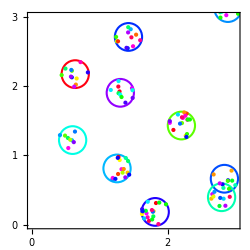

```mathematica
frame= Plot[{},{x,0,7},PlotRange->{{0,3},{0,3}},Frame->True,AspectRatio->1,FrameStyle->Directive[18,"Calibri"],ImageSize->250,FrameTicks->{{{0,1,2,3},None},{{0,1,2,3},None}}];
patch = Table[Graphics[{Hue[patchxyq[[i,3]]],AbsoluteThickness[1.5],Circle[patchxy[[i]],λ]}],{i,γ Lsize^2 }];
ru= Table[Graphics[{Hue[resunit[[i,6]]],Point[resunit[[i,{4,5}]]]}],{i,Ceiling@totru}];

f3 = Show[frame,patch,ru,FrameStyle->Directive[fs,Black,"Arial"]]
```

### Aggreg

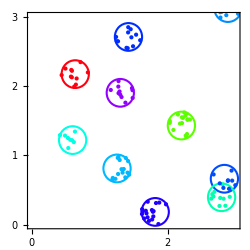

```mathematica
frame= Plot[{},{x,0,7},PlotRange->{{0,3},{0,3}},Frame->True,AspectRatio->1,FrameStyle->Directive[18,"Calibri"],ImageSize->250,FrameTicks->{{{0,1,2,3},None},{{0,1,2,3},None}}];
patch = Table[Graphics[{Hue[patchxyq[[i,3]]],AbsoluteThickness[1.5],Circle[patchxy[[i]],λ]}],{i,γ Lsize^2 }];
ru= Table[Graphics[{Hue[resunit[[i,3]]],Point[resunit[[i,{4,5}]]]}],{i,Ceiling@totru}];

f3agg = Show[frame,patch,ru,FrameStyle->Directive[fs,Black,"Arial"]]
```

### Low tau

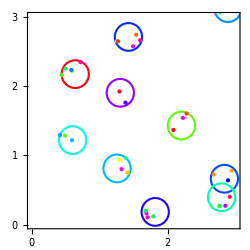

```mathematica
frame= Plot[{},{x,0,7},PlotRange->{{0,3},{0,3}},Frame->True,AspectRatio->1,FrameStyle->Directive[18,"Calibri"],ImageSize->250,FrameTicks->{{{0,1,2,3},None},{{0,1,2,3},None}}];
patch = Table[Graphics[{Hue[patchxyq[[i,3]]],AbsoluteThickness[1.5],Circle[patchxy[[i]],λ]}],{i,γ Lsize^2 }];
ru= Table[Graphics[{Hue[resunit[[i,6]]],Point[resunit[[i,{4,5}]]]}],{i,Ceiling@totru/4}];

f4= Show[frame,patch,ru,FrameStyle->Directive[fs,Black,"Arial"]]
```

### Low lambda

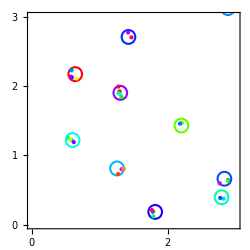

```mathematica
lru ={};newλ = 0.1;
Do[
px =  resunit[[i,1]];
py =  resunit[[i,2]];

rx =  resunit[[i,4]];
ry =  resunit[[i,5]];

dx = Abs[px- rx];
dy = Abs[py- ry];

If[Sqrt[dx^2 + dy^2] ≤ newλ,
AppendTo[lru, resunit[[i]]]
];
,{i,Length@resunit}];

frame= Plot[{},{x,0,7},PlotRange->{{0,3},{0,3}},Frame->True,AspectRatio->1,FrameStyle->Directive[18,"Calibri"],ImageSize->250,FrameTicks->{{{0,1,2,3},None},{{0,1,2,3},None}}];
patch = Table[Graphics[{Hue[patchxyq[[i,3]]],AbsoluteThickness[1.5],Circle[patchxy[[i]],newλ]}],{i,γ Lsize^2 }];
ru= Table[Graphics[{Hue[lru[[i,6]]],Point[lru[[i,{4,5}]]]}],{i,Length@lru}];

f5= Show[frame,patch,ru,FrameStyle->Directive[fs,Black,"Arial"]]
```

### Low gamma

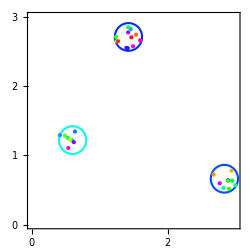

```mathematica
gru ={}; newpatchxyq = Delete[patchxyq,{{4},{9},{20},{21},{-7},{-9},{-14}}]; 
Do[
pxy =  resunit[[i,{1,2}]];

If[pxy ≠  patchxyq[[4,{1,2}]] && pxy ≠ patchxyq[[20,{1,2}]] && pxy ≠ patchxyq[[21,{1,2}]]&& pxy ≠ patchxyq[[-7,{1,2}]]&& pxy ≠ patchxyq[[9,{1,2}]]&& pxy ≠ patchxyq[[-9,{1,2}]]&& pxy ≠ patchxyq[[-14,{1,2}]],
AppendTo[gru, resunit[[i]]]
];
,{i,Length@resunit}];

frame= Plot[{},{x,0,7},PlotRange->{{0,3},{0,3}},Frame->True,AspectRatio->1,FrameStyle->Directive[18,"Calibri"],ImageSize->250,FrameTicks->{{{0,1,2,3},None},{{0,1,2,3},None}}];
patch = Table[Graphics[{Hue[newpatchxyq[[i,3]]],AbsoluteThickness[1.5],Circle[newpatchxyq[[i,{1,2}]],λ]}],{i,Length[newpatchxyq] }];
ru= Table[Graphics[{Hue[gru[[i,6]]],Point[gru[[i,{4,5}]]]}],{i,Length@gru}];

f6= Show[frame,patch,ru,FrameStyle->Directive[fs,Black,"Arial"]]
```

```mathematica
Export[localdir<>"fig1a.jpg",f3,ImageResolution->200];
Export[localdir<>"fig1c.jpg",f3agg,ImageResolution->200];
Export[localdir<>"fig1d.jpg",f4,ImageResolution->200];
Export[localdir<>"fig1e.jpg",f5,ImageResolution->200];
Export[localdir<>"fig1f.jpg",f6,ImageResolution->200];
```

## Figure 1fitness

```mathematica
Fitness[q_,nu_,qq_]:=If [nu≠Infinity,Exp[(1/nu) Cos[2 Pi q- 2 Pi qq]]/( BesselI[0,1/nu]),1];
```

```mathematica
style={{GrayLevel[gl],AbsoluteThickness[th]},{GrayLevel[gl],AbsoluteDashing[{8,8}](*,Dotted*),AbsoluteThickness[th]},{GrayLevel[gl],AbsoluteThickness[th]}};i=1;pp3={};
Do[
aa=Plot[Table[Fitness[q,extraparam,qq],{qq,Range[0,4,1/4]}],{q,0,1}, (*ColorFunction->(Hue[#1]&),*)PlotStyle->style[[i]],LabelStyle->Directive[fs]];
i++;
AppendTo[pp3,aa];
,{extraparam,{0.125,1.}}]
```

```mathematica
col=Plot[-0.08,{q,0,1}, ColorFunction->(Hue[#1]&),PlotStyle->AbsoluteThickness[4.2]];
gen =Plot[1,{q,0,1},PlotStyle->{Black,AbsoluteThickness[th+1]}];
```

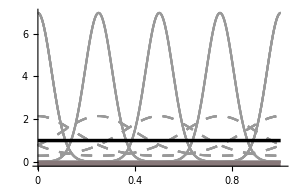

```mathematica
fig1c=Show[pp3,gen,col,LabelStyle->as,PlotRangePadding->0,PlotRange->{{0,1.01},{-0.2,7}},AxesOrigin->{0,-0.2},AxesStyle->as,Ticks->{{0,0.2,0.4,0.6,0.8,1},{0,2,4,6}}]
```

```mathematica
Export["C:\\Users\\tramiada\\Documents\\Projects\\PhD project\\generalist_specialist\\Figure1\\fig1c.jpg",fig1c,ImageResolution->200]
```

C:\Users\tramiada\Documents\Projects\PhD project\generalist_specialist\Figure1\fig1c.jpg

```mathematica
Log@BesselI[0,1/0.125]
```

6.0581

```mathematica
0.23591435850717854
```

```mathematica
Log@BesselI[0,1/0.03125]
```

29.3522

```mathematica
29.35216289102979
```

```mathematica
Log@BesselI[0,1./(10/16)]
```

0.559605

## Figure 1 B

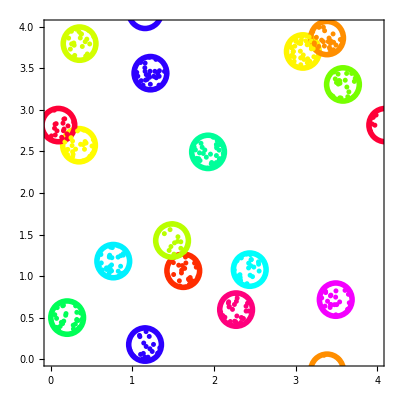

```mathematica
size= 4; lambda= 0.2;Fig= {};

dap=Import["C:\\Users\\tramiada\\Documents\\Projects\\PhD project\\generalist_specialist\\Figure1\\patch data_fig1b.csv"];
das=Import["C:\\Users\\tramiada\\Documents\\Projects\\PhD project\\generalist_specialist\\Figure1\\resource unit data_fig1b.csv"];

Do[
xx=dap[[i,1]];
yy=dap[[i,2]];
zz=dap[[i,3]];
If[xx<lambda,
AppendTo[dap,{xx+size,yy,zz}]];
If[size-xx<lambda,
AppendTo[dap,{xx-size,yy,zz}]];
If[yy<lambda,
AppendTo[dap,{xx,yy+size,zz}]];
If[size-yy<lambda,
AppendTo[dap,{xx,yy-size,zz}]];
If[xx<lambda && yy<lambda,
AppendTo[dap,{xx+lambda,yy+lambda,zz}]];
If[xx-size<lambda &&yy-size<lambda,
AppendTo[dap,{xx-size,yy-size,zz}]
];
,{i,Length[dap]}];

f1=Show[Graphics[Table[{Thickness[0.01],Hue[dap[[i,3]]],Circle[dap[[i,{1,2}]],lambda]},{i,Length[dap]}],PlotRange->{{0,size},{0,size}},PlotRangeClipping->True]];
f2=Show[Graphics[Table[{Hue[das[[i,3]]],Disk[das[[i,{1,2}]],0.03]},{i,Length[das]}],PlotRange->{{0,size},{0,size}},PlotRangeClipping->True]];
figure1=Show[f1,Frame->True,FrameStyle->Directive[asz,Black,"Arial"]];

figure2=Show[f2,Frame->True,FrameStyle->Directive[asz,Black,"Arial"]];
fig1b =Show[figure1,figure2,FrameStyle->Directive[asz,Black,AbsoluteThickness[th ],"Arial"]]
```

```mathematica
Export["C:\\Users\\tramiada\\Documents\\Projects\\PhD project\\generalist_specialist\\Figure1\\fig1b.jpg",fig1b,ImageResolution->200]
```

C:\Users\tramiada\Documents\Projects\PhD project\generalist_specialist\Figure1\fig1b.jpg